## test for homogeneous traveltime

```mathematica
Clear["Global`*"]
```

```mathematica
param={eta->0.2,t0->1,vn->2}
```

{eta→0.2,t0→1,vn→2}

```mathematica
Xp=((1+2 eta) p t0 vn^2 √(((1+2 eta) (-1+2 eta (-1+(1+2 eta) p^2 vn^2)))/(-1+(1+2 eta) p^2 vn^2)))/((1-2 eta (-1+(1+2 eta) p^2 vn^2))^2);
```

```mathematica
TT30=√(t0^2+x^2/vn^2-(4 eta x^4)/(vn^4 (t0^2+((B1) x^2)/vn^2+√(t0^4+(2 (B1)t0^2* x^2)/vn^2+(C1*x^4)/vn^4))))/.B1->2.0972196513682837/.C1->0.48636336433745453;
```

```mathematica
TT3=√(t0^2+x^2/vn^2-(4 eta x^4)/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) *t0^2*x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))));
```

```mathematica
TTe=√(t0^2 (√(((1+2 eta) (-1+(1+2 eta) p^2 vn^2))/(-1+2 eta (-1+(1+2 eta) p^2 vn^2)))+((1+2 eta) p^2 vn^2 √(((1+2 eta) (-1+2 eta (-1+(1+2 eta) p^2 vn^2)))/(-1+(1+2 eta) p^2 vn^2)))/((1-2 eta (-1+(1+2 eta) p^2 vn^2))^2))^2);
```

```mathematica
YY=x/(t0*vn)/.x->Xp;
```

```mathematica
pp1=Abs[(TTe-TT30)]*100/TTe/.x->Xp;
pp2=Abs[(TTe-TT3)]*100/TTe/.x->Xp;
```

```mathematica
{a00=ParametricPlot[{YY/.param,pp1/.param},{p,0,0.9},PlotStyle->{Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,0.03}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"GMA_01"},Right]],
a01=ParametricPlot[{YY/.param,pp2/.param},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,0.03}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"GMA"},Right]]};
```

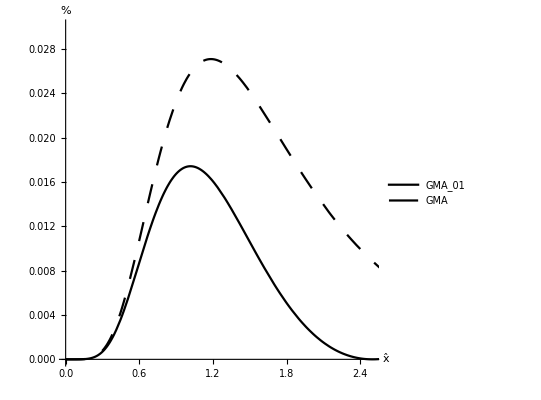

```mathematica
Show[a00,a01]
```

```mathematica
GS1id=((1/x)*D[TT30,x]*(D[TT30,{x,2}]))^(-1/2);
```

```mathematica
GS2id=((1/x)*D[TT3,x]*(D[TT3,{x,2}]))^(-1/2);
```

```mathematica
GSe=Sqrt[(Xp/p)*D[Xp,p]];
```

### for direct GMA

```mathematica
p3=√(3/(8 (eta+2 eta^2) vn^2)+eta/((eta+2 eta^2) vn^2)+1/2 √(-(3 (1+4 eta))/(4 eta^2 (1+2 eta) vn^4)+(-3-8 eta)^2/(16 (eta+2 eta^2)^2 vn^4)+(eta vn^4 X^2+4 eta^2 vn^4 X^2)/(4 (eta^3 vn^8 X^2+2 eta^4 vn^8 X^2))+((-3 eta^2 t0^2 vn^10 X^2-8 eta^3 t0^2 vn^10 X^2) (eta^9 vn^24 X^6+6 eta^10 vn^24 X^6+12 eta^11 vn^24 X^6+8 eta^12 vn^24 X^6)^(1/3))/(2^(2/3) eta^6 (1+2 eta)^2 vn^16 X^4 (216 eta^3 t0^4 vn^16 X^2+432 eta^4 t0^4 vn^16 X^2-216 eta^3 t0^2 vn^14 X^4+√(46656 eta^6 t0^8 vn^32 X^4+186624 eta^7 t0^8 vn^32 X^4+186624 eta^8 t0^8 vn^32 X^4+93312 eta^6 t0^6 vn^30 X^6+1306368 eta^7 t0^6 vn^30 X^6+3981312 eta^8 t0^6 vn^30 X^6+3538944 eta^9 t0^6 vn^30 X^6+46656 eta^6 t0^4 vn^28 X^8))^(1/3))+(216 eta^3 t0^4 vn^16 X^2+432 eta^4 t0^4 vn^16 X^2-216 eta^3 t0^2 vn^14 X^4+√(46656 eta^6 t0^8 vn^32 X^4+186624 eta^7 t0^8 vn^32 X^4+186624 eta^8 t0^8 vn^32 X^4+93312 eta^6 t0^6 vn^30 X^6+1306368 eta^7 t0^6 vn^30 X^6+3981312 eta^8 t0^6 vn^30 X^6+3538944 eta^9 t0^6 vn^30 X^6+46656 eta^6 t0^4 vn^28 X^8))^(1/3)/(24 2^(1/3) (eta^9 vn^24 X^6+6 eta^10 vn^24 X^6+12 eta^11 vn^24 X^6+8 eta^12 vn^24 X^6)^(1/3)))-1/2 √(-(3 (1+4 eta))/(4 eta^2 (1+2 eta) vn^4)+(-3-8 eta)^2/(8 (eta+2 eta^2)^2 vn^4)-(eta vn^4 X^2+4 eta^2 vn^4 X^2)/(4 (eta^3 vn^8 X^2+2 eta^4 vn^8 X^2))-((-3 eta^2 t0^2 vn^10 X^2-8 eta^3 t0^2 vn^10 X^2) (eta^9 vn^24 X^6+6 eta^10 vn^24 X^6+12 eta^11 vn^24 X^6+8 eta^12 vn^24 X^6)^(1/3))/(2^(2/3) eta^6 (1+2 eta)^2 vn^16 X^4 (216 eta^3 t0^4 vn^16 X^2+432 eta^4 t0^4 vn^16 X^2-216 eta^3 t0^2 vn^14 X^4+√(46656 eta^6 t0^8 vn^32 X^4+186624 eta^7 t0^8 vn^32 X^4+186624 eta^8 t0^8 vn^32 X^4+93312 eta^6 t0^6 vn^30 X^6+1306368 eta^7 t0^6 vn^30 X^6+3981312 eta^8 t0^6 vn^30 X^6+3538944 eta^9 t0^6 vn^30 X^6+46656 eta^6 t0^4 vn^28 X^8))^(1/3))-(216 eta^3 t0^4 vn^16 X^2+432 eta^4 t0^4 vn^16 X^2-216 eta^3 t0^2 vn^14 X^4+√(46656 eta^6 t0^8 vn^32 X^4+186624 eta^7 t0^8 vn^32 X^4+186624 eta^8 t0^8 vn^32 X^4+93312 eta^6 t0^6 vn^30 X^6+1306368 eta^7 t0^6 vn^30 X^6+3981312 eta^8 t0^6 vn^30 X^6+3538944 eta^9 t0^6 vn^30 X^6+46656 eta^6 t0^4 vn^28 X^8))^(1/3)/(24 2^(1/3) (eta^9 vn^24 X^6+6 eta^10 vn^24 X^6+12 eta^11 vn^24 X^6+8 eta^12 vn^24 X^6)^(1/3))+(-(-3-8 eta)^3/(8 (eta+2 eta^2)^3 vn^6)+(3 (-3-8 eta) (1+4 eta))/(2 eta^2 (1+2 eta) (eta+2 eta^2) vn^6)-(-t0^2 vn^2-X^2-8 eta X^2)/(eta^3 (1+2 eta) vn^6 X^2))/(4 √(-(3 (1+4 eta))/(4 eta^2 (1+2 eta) vn^4)+(-3-8 eta)^2/(16 (eta+2 eta^2)^2 vn^4)+(eta vn^4 X^2+4 eta^2 vn^4 X^2)/(4 (eta^3 vn^8 X^2+2 eta^4 vn^8 X^2))+((-3 eta^2 t0^2 vn^10 X^2-8 eta^3 t0^2 vn^10 X^2) (eta^9 vn^24 X^6+6 eta^10 vn^24 X^6+12 eta^11 vn^24 X^6+8 eta^12 vn^24 X^6)^(1/3))/(2^(2/3) eta^6 (1+2 eta)^2 vn^16 X^4 (216 eta^3 t0^4 vn^16 X^2+432 eta^4 t0^4 vn^16 X^2-216 eta^3 t0^2 vn^14 X^4+√(46656 eta^6 t0^8 vn^32 X^4+186624 eta^7 t0^8 vn^32 X^4+186624 eta^8 t0^8 vn^32 X^4+93312 eta^6 t0^6 vn^30 X^6+1306368 eta^7 t0^6 vn^30 X^6+3981312 eta^8 t0^6 vn^30 X^6+3538944 eta^9 t0^6 vn^30 X^6+46656 eta^6 t0^4 vn^28 X^8))^(1/3))+(216 eta^3 t0^4 vn^16 X^2+432 eta^4 t0^4 vn^16 X^2-216 eta^3 t0^2 vn^14 X^4+√(46656 eta^6 t0^8 vn^32 X^4+186624 eta^7 t0^8 vn^32 X^4+186624 eta^8 t0^8 vn^32 X^4+93312 eta^6 t0^6 vn^30 X^6+1306368 eta^7 t0^6 vn^30 X^6+3981312 eta^8 t0^6 vn^30 X^6+3538944 eta^9 t0^6 vn^30 X^6+46656 eta^6 t0^4 vn^28 X^8))^(1/3)/(24 2^(1/3) (eta^9 vn^24 X^6+6 eta^10 vn^24 X^6+12 eta^11 vn^24 X^6+8 eta^12 vn^24 X^6)^(1/3))))));
```

```mathematica
Lon=(t0 vn^2 √(1+4 eta p^2 vn^2-6 eta p^4 vn^4-12 eta^2 p^4 vn^4))/((1-2 eta p^2 vn^2)^2 (1-(1+2 eta) p^2 vn^2));
```

```mathematica
GS1=Lon/.p->p3;
```

```mathematica
DGS1=D[GS1,X];
```

```mathematica
AA0=t0 vn^2;
AA2=-(-1-8 eta)/t0;
AA4=-(9 (eta+4 eta^2))/(t0^3 vn^2);
```

```mathematica
BB2=(-(DGS1-2 AA2 x)/(2 AA0 x-2 GS1 x+DGS1 x^2))+(-(2 x^2*AA4)/(AA0-GS1+AA2 x^2))/.x->X;
```

```mathematica
BB4=((DGS1-2 AA2 x)^2/(x^2 (2 AA0-2 GS1+DGS1 x)^2))+((4*AA4)/(AA0-GS1+AA2 x^2))/.x->X;
```

```mathematica
BB2/.param/.X->5
```

0.762267

```mathematica
BB4/.param/.X->5
```

0.0251836

```mathematica
GMA0=AA0+AA2*x^2+2*AA4*x^4/(1+BB2*x^2+Sqrt[1+2*BB2*x^2+BB4*x^4])/.x->Xp/.BB2->0.7622670899797642/.BB4->0.025183642832786617;
```

```mathematica
C0=((1+6 eta) t0 vn^2)/(1/(1+2 eta))^(3/2);
C2=(√(1/(1+2 eta)))/t0;
BBB2=(AA2^2-2 AA0 AA4+2 AA4 C0-2 AA2 C2+C2^2)/((AA0-C0) (AA2-C2));
BBB4=(AA2-C2)^2/(AA0-C0)^2;
GMA1=AA0+AA2 x^2+(2 AA4 x^4)/(1+BBB2 x^2+√(1+2 BBB2 x^2+BBB4 x^4));
```

```mathematica
bb1id=Abs[(GSe-GS1id)]*100/GSe/.x->Xp;
bb2id=Abs[(GSe-GS2id)]*100/GSe/.x->Xp;
```

```mathematica
bb1d=Abs[(Lon-GMA0)]*100/Lon/.x->Xp;
bb2d=Abs[(Lon-GMA1)]*100/Lon/.x->Xp;
```

```mathematica
{b000=ParametricPlot[{YY/.param,bb1id/.param},{p,0,0.9},PlotStyle->{Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,0.4}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"id_GMA_X"},Right]],
b011=ParametricPlot[{YY/.param,bb2id/.param},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,0.4}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"id_GMA_∞"},Right]],b012=ParametricPlot[{YY/.param,bb1d/.param},{p,0,0.9},PlotStyle->{Directive[DotDashed,Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,0.4}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"d_GMA_X"},Right]],b013=ParametricPlot[{YY/.param,bb2d/.param},{p,0,0.9},PlotStyle->{Directive[Dotted,Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,0.4}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"d_GMA_∞"},Right]]};
```

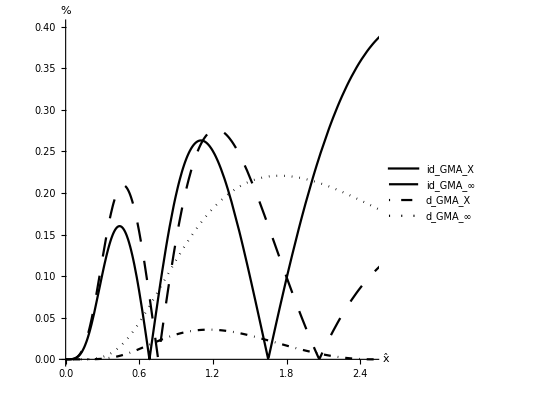

```mathematica
Show[b000,b011,b012,b013]
```